(c ⅇ^(-r^2/2))/(2 √2 π^(3/2))+d1 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r

{c→-43.2037}

{c→-40.2833,d1→2.36456,d2→0.}

Function[r,-2.74316 ⅇ^(-r^2/2)-Erf[r/(√2)]/r]

Function[r,-2.55773 ⅇ^(-r^2/2)+2.36456 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r]

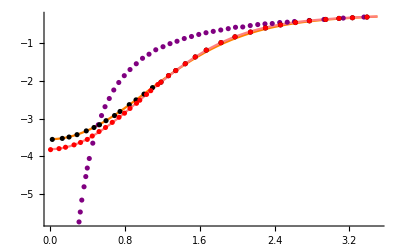

```mathematica
TrueV=Import["C:\\Users\\ASUS\\Documents\\Lepage_TrueV.dat","CSV"];
VeLO=Import["C:\\Users\\ASUS\\Documents\\Lepage_VeLO.dat","CSV"];
VeNLO=Import["C:\\Users\\ASUS\\Documents\\Lepage_VeNLO.dat","CSV"];
α=1;a=1;
(*ModelVeLO1=- α/rErf[r/(√2 a)]+c a^2 DiracDelta[r];*)
ModelVeLO=- α/r Erf[r/(√2 a)]+c a^2 (E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);
ModelVeNLO=-α/r Erf[r/(√2 a)]+c a^2 (E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3)+d1 a^4 Laplacian[(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3),{r,θ,ϕ},"Spherical"]
(*+d2 a^4 Div[(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3),{r,θ,ϕ},"Spherical"]*)
(*ModelVeNLO1=-α/r(*Erf[r/(√2 a)]*)+(*c a^2 (E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3)+d1 a^4 Laplacian[(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3),{r,θ,ϕ},"Spherical"]+*)d2 r*)
FitVeLO=FindFit[VeLO,ModelVeLO,{(*a,*)c},r]
(*FitVeLO1=FindFit[VeLO,ModelVeLO1,{a,c},r]*)
FitVeNLO=FindFit[VeNLO,ModelVeNLO,{(*a,*)c,d1,d2},r]
(*FitVeNLO1=FindFit[VeNLO,ModelVeNLO1,{a,c,d1,d2},r]*)
VeLOf=Function[r,Evaluate[ModelVeLO/.FitVeLO]]
(*VeLOf1=Function[r,Evaluate[ModelVeLO1/.FitVeLO1]]*)
VeNLOf=Function[r,Evaluate[ModelVeNLO/.FitVeNLO]]
(*VeNLOf1=Function[r,Evaluate[ModelVeNLO1/.FitVeNLO1]]*)
Show[Plot[{VeLOf[r],VeNLOf[r]},{r,0.01,3.5},PlotStyle->{Orange,Pink}](*,Plot[VeNLOf[r],{r,0.01,3.5},Epilog->Map[Point,VeNLO]]*),ListPlot[{TrueV,VeLO,VeNLO},PlotStyle->{Purple,Black,Red}],PlotRange->All(*{{0,0.5},{-3.8,-3.1}}*)]
(*Plot[{VeNLOf[r]-VeNLOf1[r]},{r,0.01,3.5},Epilog->Map[Point,VeNLO]]*)
```

```mathematica
ModelVeLO/.%91
ModelVeNLO/.%92
```

-2.74316 ⅇ^(-r^2/2)-Erf[r/(√2)]/r

-2.55773 ⅇ^(-r^2/2)+2.36456 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r

```mathematica
Div[(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3),{r,θ,ϕ},"Spherical"]
```

Div::sclr: 标量表达式 (ⅇ^(-r^2/(2 a^2)))/(2 √2 a^3 π^(3/2)) 没有散度.

Div[(ⅇ^(-r^2/(2 a^2)))/(2 √2 a^3 π^(3/2)),{r,θ,ϕ},Spherical]

```mathematica
Div[DiracDelta[r,θ,ϕ],{r,θ,ϕ},"Spherical"]
```

Div::sclr: 标量表达式 DiracDelta[r,θ,ϕ] 没有散度.

Div[DiracDelta[r,θ,ϕ],{r,θ,ϕ},Spherical]

```mathematica
Clear[a]
```